{0.797885,0.782085,0.73654,0.666449,0.579383,0.483941,0.388372,0.299455,0.221842,0.1579}

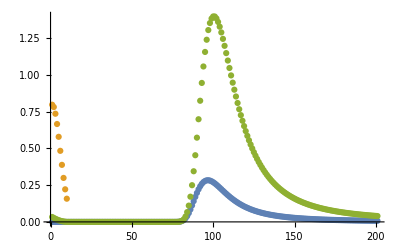

```mathematica
landau = Table[PDF[LandauDistribution[10, 1], x], {x, 0, 20, 0.1}];
gauss = Table[PDF[NormalDistribution[0, 0.5], x], {x, 0, 20, 0.1}][[;;10]]
conv = ListConvolve[gauss, landau, 1];
ListPlot[{landau, gauss, conv}, PlotRange->All]
```

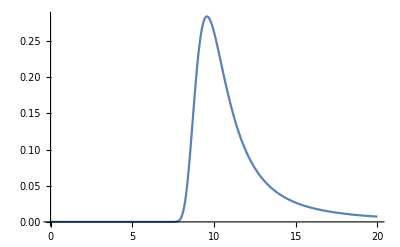

```mathematica
Plot[PDF[LandauDistribution[10, 1], x], {x, 0, 20}]
```